{{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

{{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

Ground State at test time 5 = {-0.663421,0.466418,-0.333514,0.480724}

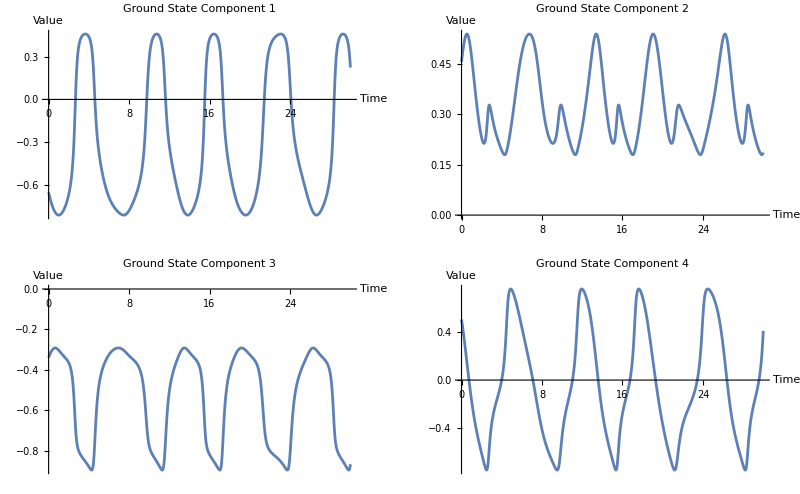

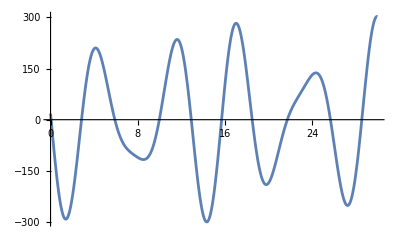

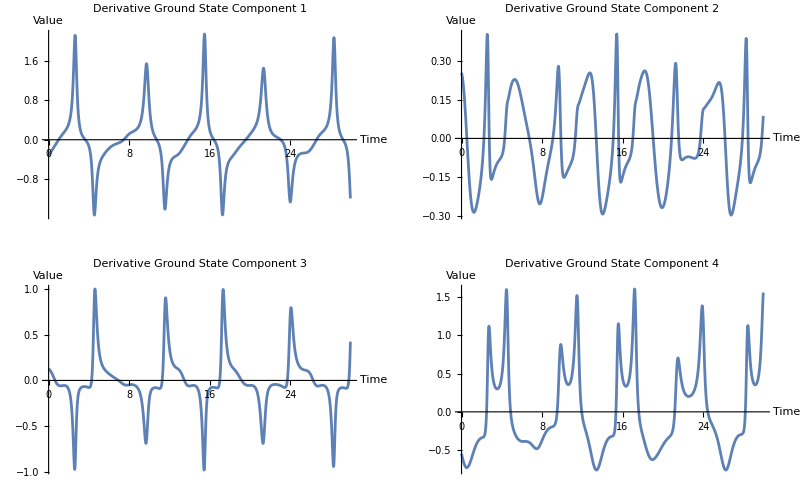

{{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

{{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

12854.6

Eigenvalues

{1223.31,838.258,374.754,-0.0331162}

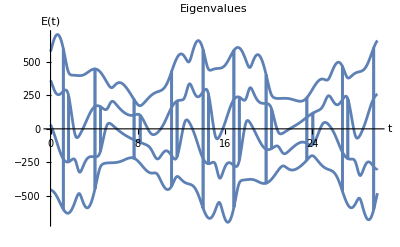

```mathematica
Needs["NumericalCalculus`"]

initialTime=0;
endTime=30;

dimension=4;
t1=1;
t2=1/Sqrt[2];
n=1000;
dt=0.01;

Tscale[T_]:=100

generateGOEMatrix[n_Integer]:=Module[{matrix},matrix=Table[If[i==j,RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,1/Sqrt[2]]]],{i,n},{j,n}];
matrix=(matrix+Transpose[matrix])/2;matrix]

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

H[t_,T_]:=Tscale[T]*((Sin[t/t1]*2.1+Sin[t/t2])*Hinitial+(Cos[t/t1]*2.7+Cos[t/t2])*Hend)

groundState[t_,T_]:=Module[{eigenvalues,eigenvectors,minIndex},{eigenvalues,eigenvectors}=Eigensystem[H[t,T]];
minIndex=First[Ordering[Re[eigenvalues],1]];
Normalize[Re[eigenvectors[[minIndex]]]]]

generateGroundStates[dt_,T_]:=Module[{t,states,currentState,nextState,dotProduct,stateTable},stateTable=Association[];
states={groundState[initialTime,T]};
stateTable[initialTime]=groundState[initialTime,T];
currentState=groundState[initialTime,T];
For[t=initialTime,t<endTime,t+=dt,nextState=groundState[t+dt,T];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];
stateTable[t+dt]=currentState;];
stateTable]

gStates=generateGroundStates[dt,Tscale];

timePoints=Keys[gStates];
groundStateComponents=Values[gStates];

testTime=5;
Print["Ground State at test time ",testTime," = ",gStates[[testTime]]];

groundStateComponentsTranspose=Transpose[groundStateComponents];


plots=Table[ListLinePlot[Transpose[{timePoints,groundStateComponentsTranspose[[i]]}],PlotRange->All,PlotLabel->"Ground State Component "<>ToString[i],AxesLabel->{"Time","Value"}],{i,dimension}];

GraphicsGrid[Partition[plots,2]]

Plot[H[t, Tscale[1]][[1, 1]], {t, initialTime, endTime}]

state[t_,n_,T_]:=Module[{eigenvalues,eigenvectors,index},{eigenvalues,eigenvectors}=Eigensystem[H[t,T]];
index=Ordering[Re[eigenvalues],n+1][[n+1]];
Normalize[Re[eigenvectors[[index]]]]]

generateExcitedStates[dt_,n_,T_]:=Module[{t,states,currentState,nextState,dotProduct},states={state[initialTime,n,T]};
currentState=state[initialTime,n,T];
For[t=initialTime,t<endTime,t+=dt,nextState=state[t+dt,n,T];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];];
states]
gap[t_,n_,T_]:=Module[{eigenvalues,sortedEigenvalues,smallestEigenvalue,nEigenvalue,difference},eigenvalues=Re[Eigenvalues[H[t,T]]];
sortedEigenvalues=Sort[eigenvalues];
smallestEigenvalue=sortedEigenvalues[[1]];
nEigenvalue=sortedEigenvalues[[n+1]];
difference=nEigenvalue-smallestEigenvalue;
difference]

omega[n_,T_]:=NIntegrate[gap[t,n,T]/Tscale[T],{t,initialTime,endTime}]

(*
derivativeGroundState[t_?NumericQ,T_,h_:0.0001]:=(groundState[t+h,T]*(groundState[t+h,T].groundState[t-h,T])-groundState[t-h,T])/(2*h)

derivativeGroundStateComponent[t_?NumericQ,T_,h_:0.01,i_]:=derivativeGroundState[t,T,h][[i]]


plots=Table[Plot[derivativeGroundStateComponent[t,Tscale[1],0.01,i],{t,initialTime,endTime},PlotLabel->"Derivative Ground State Component "<>ToString[i],AxesLabel->{"Time","Value"},PlotRange->All],{i,1,dimension}];

GraphicsGrid[Partition[plots,2]]
*)

derivativeGroundStateDiscrete[gStates_,dt_]:=Module[{times,states,derivativeStates},times=Keys[gStates];
states=Values[gStates];
derivativeStates=Table[(states[[i+1]]-states[[i]])/dt,{i,Length[states]-1}];
AssociationThread[Most[times]->derivativeStates]]

derivativeGroundStates=derivativeGroundStateDiscrete[gStates,dt];

timePointsDerivative=Keys[derivativeGroundStates];
derivativeComponents=Values[derivativeGroundStates];
derivativeComponentsTranspose=Transpose[derivativeComponents];

plots=Table[ListLinePlot[Transpose[{timePointsDerivative,derivativeComponentsTranspose[[i]]}],PlotRange->All,PlotLabel->"Derivative Ground State Component "<>ToString[i],AxesLabel->{"Time","Value"}],{i,dimension}];

GraphicsGrid[Partition[plots,2]]


normDerivativeGroundState[t_]:=Norm[derivativeGroundStates[[t]]]

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

Q =Sum[derivativeGroundStates[[Round[t*100]]].((H[t, Tscale[t]]-Dot[gStates[[Round[t*100]]],Dot[H[t, Tscale[t]],gStates[[Round[t*100]]]]]*IdentityMatrix[4]).derivativeGroundStates[[Round[t*100]]])/(derivativeGroundStates[[Round[t*100]]].derivativeGroundStates[[Round[t*100]]]*Tscale[1]), {t, initialTime+0.01, endTime, dt}]
(*Q2 =Total[Sum[derivativeGroundStates[[t*100+1]].(H[t, Tscale[t]]-gStates[[t*100+1]])*IdentityMatrix[dimension].derivativeGroundStates[[t*100+1]]/(Norm[derivativeGroundStates[[t*100+1]]]^2), {t, initialTime, endTime, dt}]]*)

(*
calculateQ[endTime_,dt_,dimension_,Tscale_,gStates_,derivativeGroundStates_]:=Module[{Q,keys,t},keys=Select[Keys[derivativeGroundStates],#<=endTime&];
Q=Sum[t=key;
derivativeGroundStates[t].(H[t,Tscale[t]]-Dot[gStates[[t*100+1]],Dot[H[t, Tscale[t]],gStates[[t*100+1]]]]*IdentityMatrix[4]).derivativeGroundStates[t]/(Norm[derivativeGroundStates[t]]^2),{key,keys}];
Print["Q[",endTime,"]: ",Q];
Q]

Qvalues=Table[Module[{gStates,derivativeGroundStates,Q},gStates=generateGroundStates[dt,Tscale];
derivativeGroundStates=derivativeGroundStateDiscrete[gStates,dt];
Q=calculateQ[endTime,dt,dimension,Tscale,gStates,derivativeGroundStates];
Q],{endTime,1,10}]

ListPlot[Qvalues,PlotRange->All,PlotLabel->"Q values for end times 1 to 10",AxesLabel->{"End Time","Q Value"}]
*)


Print["Eigenvalues"];
Eigenvalues[H[1, Tscale[1]]-Dot[gStates[[1*100]],Dot[H[1, Tscale[1]],gStates[[1*100]]]]*IdentityMatrix[4]]

Plot[Eigenvalues[H[t, Tscale[1]]],{t,initialTime,endTime},PlotRange->All,PlotLabel->"Eigenvalues",AxesLabel->{"t","E(t)"}]
```